```mathematica
f = Import["/Users/newlocaluser/Documents/MP2/Data/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciAdultNormCrossOmegas10 = Flatten[Values[Select[f,Keys[#]=="bciAdultNormCrossOmegas10"&]],1];
index14110 = Flatten[Values[Select[f,Keys[#]=="index141_10"&]]];
```

```mathematica
B=MapThread[If[#2,MapThread[If[#2,#1,0]&,{#1,index14110}],ConstantArray[0,Length[#1]]]&,{bciAdultNormCrossOmegas10,index14110}];
```

```mathematica
A = DeleteDuplicates[DeleteCases[Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>2.75 && i≠j,Min[i,j]<->Max[i,j],0]]&,#1]]&,B]],0]];
```

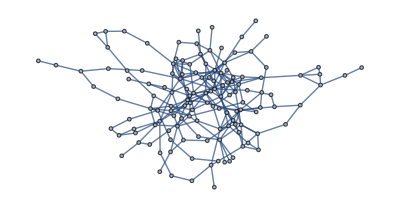

```mathematica
g =Graph[A,DirectedEdges->False]
```

{{117,200,6,70,162,7,69,141,299,17,140,255,46,297,298,58,206,180,118,145,271,295},{5,155,223,11,27,113,114,153,45,121,193,40,111,127,213,74,63,116,91,253},{32,148,192,36,183,205,71,231,241,86,108,112,203,269,124,179,208,202,296},{142,212,10,39,72,50,90,254,170,277,55,209,82,93,258,125},{2,119,265,3,132,279,19,87,110,281,131,196,260},{290,107,233,18,289,283,57,182,243,245,288,157},{48,248,161,143,204,264,291,150},{43,235,259,59,79,188,78},{252,9,34,44,64,276},{25,137,280,92,194,214},{250,83,104,232,263,266}}

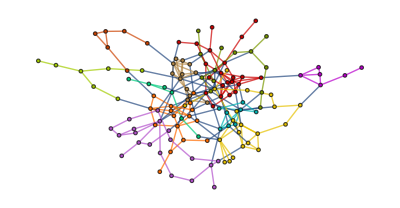

-Graphics-

```mathematica
communities = FindGraphCommunities[g]
HighlightGraph[g,Map[Subgraph[g,#]&,communities]]
CommunityGraphPlot[g,communities]
```

```mathematica
Length[communities]
ColorData[0,"ColorList"]
```

11

ColorData::notent: 0 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData[0,ColorList]

```mathematica
bciTraits = Import["/Users/newlocaluser/Documents/MP2/Data/David Data/bci.traits.csv"];
```

```mathematica
ValidData[var_] := Not[MemberQ[Map[NumberQ[#]&,var],False]]
```

```mathematica
If[ValidData[{1,2,3}],1,0]
```

1

```mathematica
ReducedData = DimensionReduce[DeleteCases[Map[If[ValidData[Take[#,-3]],Take[#,{6,25}],Invalid]&,bciTraits],Invalid],3];
```

```mathematica
Graphics3D[Map[Point[#]&,ReducedData],Axes->True]
```

-Graphics3D-